# Día 1 - Introducción al lenguaje

## Introducción

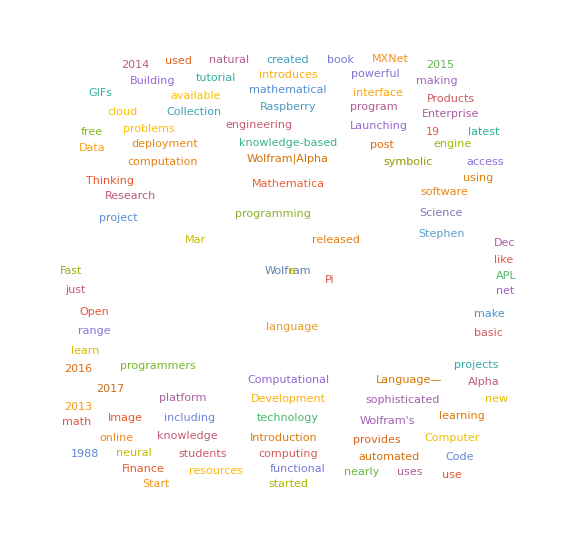

```mathematica
googleCS=ServiceConnect["GoogleCustomSearch"];
results=googleCS["Search",{"Query"->"Wolfram language",MaxItems->200}];
WordCloud[DeleteStopwords[Flatten[Join[Map[TextWords,Normal[results[All,"Snippet"]]]]]]]
```

## Un lenguaje con un paradigma:

Posiblemente el lenguaje de más alto nivel

Fuente: http://blog.wolfram.com/2016/11/09/the-2016-wolfram-one-liner-competition-winners/

```mathematica
i = RandomImage[];
Dynamic[Magnify[i = NetInitialize[NetChain[{ConvolutionLayer[3,3],Tanh},"Input"->"Image","Output"->"Image"]][i],3]]
```

Todo es una expresión simbólica

```mathematica
imagen = -Graphics-;
```

```mathematica
ImageRotate[imagen,π/6]
```

-Graphics-

```mathematica
val = 1.9;
ImageTransformation[imagen,{Re[#],Im[#]}&[val/(1+I-val{1,I}.#)]&,600,Padding->"Reflected"]
```

-Graphics-

Funcional

```mathematica
a = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Map[#^2&,a]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
b = Partition[Range[20],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20}}

```mathematica
MapAt[#^2&,b,{All,2}]
```

{{1,4},{3,16},{5,36},{7,64},{9,100},{11,144},{13,196},{15,256},{17,324},{19,400}}

Basado en el conocimiento

WolframAlphaQueryParseResults

-Graphics-

WolframAlphaQueryParseResults

Xalapa

```mathematica
CityData[Entity["City",{"Xalapa","Veracruz","Mexico"}],"Coordinates"]
```

{19.53,-96.92}

```mathematica
Entity["City",{"Xalapa","Veracruz","Mexico"}]["Population"]
```

387879 people

```mathematica
EntityList[EntityClass["Country","Countries"]]
```

{Afghanistan,Aland Islands,Albania,Algeria,American Samoa,Andorra,Angola,Anguilla,Antigua and Barbuda,Argentina,Armenia,Aruba,Australia,Austria,Azerbaijan,Bahamas,Bahrain,Bangladesh,Barbados,Belarus,Belgium,Belize,Benin,Bermuda,Bhutan,Bolivia,Caribbean Netherlands,Bosnia and Herzegovina,Botswana,Bouvet Island,Brazil,British Indian Ocean Territory,British Virgin Islands,Brunei,Bulgaria,Burkina Faso,Burundi,Cambodia,Cameroon,Canada,Cape Verde,Cayman Islands,Central African Republic,Chad,Chile,China,Christmas Island,Cocos Keeling Islands,Colombia,Comoros,Cook Islands,Costa Rica,Croatia,Cuba,Curacao,Cyprus,Czech Republic,Democratic Republic of the Congo,Denmark,Djibouti,Dominica,Dominican Republic,East Timor,Ecuador,Egypt,El Salvador,Equatorial Guinea,Eritrea,Estonia,Ethiopia,Falkland Islands,Faroe Islands,Fiji,Finland,France,French Guiana,French Polynesia,French Southern And Antarctic lands,Gabon,Gambia,Gaza Strip,Georgia,Germany,Ghana,Gibraltar,Greece,Greenland,Grenada,Guadeloupe,Guam,Guatemala,Guernsey,Guinea,Guinea-Bissau,Guyana,Haiti,Honduras,Hong Kong,Hungary,Iceland,India,Indonesia,Iran,Iraq,Ireland,Isle of Man,Israel,Italy,Ivory Coast,Jamaica,Japan,Jersey,Jordan,Kazakhstan,Kenya,Kiribati,Kosovo,Kuwait,Kyrgyzstan,Laos,Latvia,Lebanon,Lesotho,Liberia,Libya,Liechtenstein,Lithuania,Luxembourg,Macau,Macedonia,Madagascar,Malawi,Malaysia,Maldives,Mali,Malta,Marshall Islands,Martinique,Mauritania,Mauritius,Mayotte,Mexico,Micronesia,Moldova,Monaco,Mongolia,Montenegro,Montserrat,Morocco,Mozambique,Myanmar,Namibia,Nauru,Nepal,Netherlands,New Caledonia,New Zealand,Nicaragua,Niger,Nigeria,Niue,Norfolk Island,Northern Mariana Islands,North Korea,Norway,Oman,Pakistan,Palau,Panama,Papua New Guinea,Paraguay,Peru,Philippines,Pitcairn Islands,Poland,Portugal,Puerto Rico,Qatar,Republic of the Congo,Réunion,Romania,Russia,Rwanda,Saint Barthelemy,Saint Helena, Ascension and Tristan da Cunha,Saint Kitts and Nevis,Saint Lucia,Saint Martin,Saint Pierre and Miquelon,Saint Vincent and the Grenadines,Samoa,San Marino,São Tomé and Príncipe,Saudi Arabia,Senegal,Serbia,Seychelles,Sierra Leone,Singapore,Sint Maarten,Slovakia,Slovenia,Solomon Islands,Somalia,South Africa,South Georgia and the South Sandwich Islands,South Korea,South Sudan,Spain,Sri Lanka,Sudan,Suriname,Svalbard,Swaziland,Sweden,Switzerland,Syria,Taiwan,Tajikistan,Tanzania,Thailand,Togo,Tokelau,Tonga,Trinidad and Tobago,Tunisia,Turkey,Turkmenistan,Turks and Caicos Islands,Tuvalu,Uganda,Ukraine,United Arab Emirates,United Kingdom,United States,United States Minor Outlying Islands,United States Virgin Islands,Uruguay,Uzbekistan,Vanuatu,Vatican City,Venezuela,Vietnam,Wallis and Futuna Islands,West Bank,Western Sahara,Yemen,Zambia,Zimbabwe}

```mathematica
EntityList["Planet"]
```

{Mercury,Venus,Earth,Mars,Jupiter,Saturn,Uranus,Neptune}

Interactivo

```mathematica
a = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Manipulate[Map[#^i&,a],{i,1,2}]
```

```mathematica
Manipulate[ListPlot[Map[#^i&,a],PlotRange->{{0,11},{0,100}}],{i,1,2}]
```

## Síntaxis básica y funciones

### Expresiones

En la interfaz notebook de Mathematica existen dos tipos de entrada: código y texto. Las opciones para alternar entre código y texto se encuentran en Format -> Style. El código se puede ejecutar con Shift+Enter. La interfaz de notebook actúa como un front-end, que se encarga de enviar el código ejecutado al kernel.

En el lenguaje Wolfram todo son expresiones. Las expresiones pueden consistir en números como:

Enteros

```mathematica
5
```

5

Números reales

```mathematica
230.4
```

230.4

Números complejos

```mathematica
2+ⅈ
```

2+ⅈ

Racionales

```mathematica
3/2
```

3/2

Cadenas de texto:

```mathematica
"Hello world"
```

Hello world

Y símbolos, los cuales se pueden asignar

```mathematica
x
```

x

```mathematica
α = 1
```

1

```mathematica
α
```

1

Nota, para introducir los símbolos especiales se usa la tecla Esc. Por ejempllo, para α se pulsa Esc + a + Esc.

Es muy importante hacer notar que como todos son expresiones, todo, incluso los símbolos. Es por eso que es posible dar un símbolo no asignado como argumento de una función.

```mathematica
f[x]
```

f[x]

```mathematica
NestList[f,x,5]
```

{x,f[x],f[f[x]],f[f[f[x]]],f[f[f[f[x]]]],f[f[f[f[f[x]]]]]}

Al asignar una expresión esta se guarda en el espacio global del kernel. Si es necesario se puede borrar la definición usando la función Clear.

```mathematica
Clear[α]
```

Para realizar cálculos numéricos no es recomendable el uso de números racionales. Para convertir estos en números reales se utiliza la función N.

```mathematica
N[4/9]
```

0.444444

Para ocultar el resultado escribimos punto y coma al final del statement.

```mathematica
var = 6;
```

### Propiedades de las expresiones

A este tipo de elementos se les denomina expresiones atómicas, esto es, expresiones que no pueden ser subdivididas. Una manera de conocer si una expresión es atómica es usando la función AtomQ.

```mathematica
AtomQ[x]
```

True

```mathematica
AtomQ[x+3]
```

False

Las expresiones están compuestas por un encabezado que indica el tipo de expresión, y el contenido, el cual es manejado y optimizado por el kernel. Se puede ver el encabezado usando la función Head.

```mathematica
Head[x]
```

Symbol

```mathematica
Head[3]
```

Integer

```mathematica
Head["hello world"]
```

String

```mathematica
Head[3.3]
```

Real

### Listas

Se pueden definir listas con varios tipos de expresiones, como por ejemplo

```mathematica
list = {1,x,"a string",7/8}
```

{1,x,a string,7/8}

Cuando se define una lista se crea una expresión con el encabezado de lista,

```mathematica
Head[list]
```

List

y se puede acceder a cada elemento por su índice (comenzando a partir de 1)

```mathematica
list[[1]]
```

1

```mathematica
list[[2]]
```

x

Los índices también pueden ser negativos.

```mathematica
list[[-1]]
```

7/8

Para conocer el tamaño de una lista se usa la función Length.

```mathematica
Length[list]
```

4

Se pueden acceder a varios elementos simultáneos de una lista por medio del operador Span (  ;;  ) y del operador Part (  [[]]  ), por ejemplo

```mathematica
{a,b,c,d,e,f,g,h}[[2;;4]]
```

{{{1,2},{3,4},{5,6},{7,8},{9,10},{11,12},{13,14},{15,16},{17,18},{19,20}},c,d}

```mathematica
FullForm[Hold[{a,b,c,d,e,f,g,h}[[2;;4]]]]
```

Hold[Part[List[a,b,c,d,e,f,g,h],Span[2,4]]]

nos devuelve los elementos desde el índice 2 al índice 5. También se puede especificar el intervalo de salto, como por ejemplo, tomar los elementos del 1 al 6 dando saltos de 2 en 2.

```mathematica
{a,b,c,d,e,f,g,h}[[1;;6;;2]]
```

{{1,2,3,4,5,6,7,8,9,10},c,e}

En caso de tener listas bidimensionales se puede hacer uso de la propiedad All del operador Part para acceder a cada unas de las columnas.

```mathematica
{{1,2},{3,4},{5,6}}[[All,1]]
```

{1,3,5}

```mathematica
{{1,2,3},{4,5,6},{7,8,9}}[[All,2]]
```

{2,5,8}

Se puede también obtener varios índices específicos de las sublistas.

```mathematica
{{1,2,3},{4,5,6},{7,8,9}}[[All,{1,2}]]
```

{{1,2},{4,5},{7,8}}

#### Ejercicio

Dada la matriz

```mathematica
m=Partition[Range[12],4];
MatrixForm[m]
```

(1 | 2 | 3 | 4
5 | 6 | 7 | 8
9 | 10 | 11 | 12)

Intercambie la segunda y tercera fila, y la segunda y la tercera columna de forma que quede

```mathematica
MatrixForm[{{1,3,2,4},{9,11,10,12},{5,7,6,8}}]
```

(1 | 3 | 2 | 4
9 | 11 | 10 | 12
5 | 7 | 6 | 8)

### Reglas de estilo para listas

Al trabajar con listas es posible crear código poco legible. Un ejemplo es el siguiente:

```mathematica
list = Range[10]
{subl1,subl2,subl3} = {list[[1]],list[[2;;-1]],list[[-1]]}
```

{1,2,3,4,5,6,7,8,9,10}

{1,{2,3,4,5,6,7,8,9,10},10}

Una mejor práctica sería utilizando funciones específicas (no siempre aplica) dado que es inmediatamente claro la operación que realizan.

```mathematica
{subl1,subl2,subl3} = {First[list],Rest[list],Last[list]}
```

{1,{2,3,4,5,6,7,8,9,10},10}

### Operadores

Se pueden combinar varias expresiones por medio de operadores. Un ejemplo de operador es el símbolo de adición +. Cuando se realiza una suma, Mathematica nos devuelve el resultado.

```mathematica
2+2
```

4

o

```mathematica
x+y
```

x+y

En realidad, internamente el kernel se encarga de interpretar los operadores y por medio de una regla de sustitución reemplaza el operador por una función. La forma real de la expresión se puede obtener con la función FullForm.

```mathematica
FullForm[x+y]
```

Plus[x,y]

Nótese que el encabezado de una suma es la función Plus.

```mathematica
Head[x+y]
```

Plus

Los operadores funcionan también con expresiones más complejas.

```mathematica
FullForm[(x+y^2)*z]
```

Times[Plus[x,Power[y,2]],z]

El lenguaje Wolfram cuenta con una multitud de operadores de diversos tipos, pero se pueden dividir principalmente en tres tipos:

Operadores Prefix - Son los que preceden a una expresión

```mathematica
!False
```

True

```mathematica
f@x
```

f[x]

Y se representan internamente con

```mathematica
Prefix[f[x]]
```

f@x

Operadores Infix - Son los que se encuentran en medio de dos expresiones

```mathematica
4+5
```

9

Se representan internamente con

```mathematica
Infix[f[x,y,z],"#"]
```

x#y#z

Operadores Postfix - Se encuentran después de una expresión

```mathematica
Postfix[f[x]]
```

x//f

Cuando el kernel termina de ejecutar las funciones, devuelve los resultados en forma Prefix[], Infix[] o Postfix[], y la interfaz de notebook se encarga de darles formato.

Incluso operaciones simples como el ; al final de un statement para evitar que muestre el resultado de la evaluación es en realidad un operador que representa a la función CompoundExpression[].

```mathematica
Print[x];Print[y]
```

x

y

```mathematica
CompoundExpression[Print[x],Print[y]]
```

x

y

Nota: Hold nos ayuda a evitar que se evaluen las funciones Print, y así podemos ver la forma completa de la expresión antes de ser evaluada.

```mathematica
FullForm[Hold[Print[x];Print[y]]]
```

Hold[CompoundExpression[Print[x],Print[y]]]

### Asignaciones

Existen dos tipos de operadores de asignación. El más común es el operador de asignación instantánea, lhs = rhs, que está representado por la función Set.

```mathematica
n = 5
```

5

```mathematica
n
```

5

```mathematica
FullForm[Hold[n=5]]
```

Hold[Set[n,5]]

Se caracteriza porque una vez asignado el valor del símbolo, este no cambiará de valor a no ser que se realice otra asignación. Esto es análogo a las asignaciones en otros lenguajes de programación.
El otro operador es el de asignación retardada, lhs := rhs, que se caracteriza por mantener rhs en forma no evaluada hasta que se requiera evaluar lhs. Para entender esto veamos el siguiente ejemplo.

Al ejecutar el siguiente código,

```mathematica
n = RandomReal[]
```

0.406011

n adquiere un valor que permanece fijo.

```mathematica
n
```

0.406011

Pero con una asignación retardada, n no adquiere ningún valor específico.

```mathematica
n := RandomReal[]
```

Entonces cada vez que queramos ver el valor de n, se llamará a la función RandomReal.

```mathematica
n
```

0.581064

```mathematica
n
```

0.0329449

La convención para nombrar símbolos es usar lowerCamelCase.

### Iteradores

El lenguaje Wolfram posee funciones para iterar sobre elementos o un rango numérico. La regla general es que si uno utiliza una estructura de control tipo For, While o Do, hay un error en el diseño del código. El iterador más general es Table, que nos permite crear listas.

```mathematica
Table[i,{i,20}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Table[i^2,{i,3,10}]
```

{9,16,25,36,49,64,81,100}

Table también nos permite iterar sobre listas

```mathematica
Table[2*i,{i,{1,3,4,2}}]
```

{2,6,8,4}

#### Ejercicio 1

A partir de la lista

```mathematica
l = {1,"hola",9/8,2.3}
```

{1,hola,9/8,2.3}

crear un snippet que obtenga el encabezado (Head) de cada elemento.

#### Ejercicio 2

Crear un snippet que genera la siguiente lista

```mathematica
{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}
```

{{1,1},{2,4},{3,9},{4,16},{5,25},{6,36},{7,49},{8,64},{9,81},{10,100}}

#### Ejercicio 3

Dadas dos listas

```mathematica
a={0,1,2,3,4};
b={5,6,7,8,9};
```

Escriba el código que devuelva

```mathematica
{{0,5},{1,6},{2,7},{3,8},{4,9}}
```

{{0,5},{1,6},{2,7},{3,8},{4,9}}

Nota: Puede ser útil buscar en la documentación, pero no es necesario.

### Reglas de sustitución y patrones

Las reglas de sustitución son un aspecto central en el diseño del lenguaje Wolfram, de hecho, como se verá posteriormente, las funciones son un caso especial de una regla de sustitución con patrones. Para usar esta funcionalidad es necesario establecer una regla de sustitución que buscará un patrón. Un ejemplo de una regla de sustitución simple puede ser reemplazar todas las ocurrencias del número 1 por el número 2.

```mathematica
{1,2,3,4,1,9,8} /. 1->2
```

{2,2,3,4,2,9,8}

Hay 3 operadores básicos.     /. es el operador que representa a la función ReplaceAll, -> Representa la función Rule, y :> representa RuleDelayed. RuleDelayed es a Rule lo que SetDelayed (:=) es a Set (=).

```mathematica
FullForm[Hold[{1,2,3,4,1,9,8} /. 1->2]]
```

Hold[ReplaceAll[List[1,2,3,4,1,9,8],Rule[1,2]]]

Reemplazar una expresión por otra no es muy flexible, para eso Wolfram nos provee de una síntaxis más general.

El patrón underscore _ hace un match de cualquier tipo de expresión.

```mathematica
{1,2,3,4,1,9,8} /. _->3
```

3

```mathematica
x /. _->3
```

3

¿Para qué nos sirve este tipo de patrón? Resulta extremadamente útil cuando se requiere ignorar un elemento de una expresión. Por ejemplo

```mathematica
{{1,2},{3,7},{8,2},{5,0}} /. {_,2}->"reemplazado"
```

{reemplazado,{3,7},reemplazado,{5,0}}

El patrón x_ es similar a _ con la diferencia de que guarda temporalmente el símbolo correspondiente en x. Al reemplazar con símbolos es más recomendable usar RuleDelayed. Por ejemplo

```mathematica
{{1,2},{3,7},{8,2},{5,0}} /. {x_,2}:>{x^2,2}
```

{{1,2},{3,7},{64,2},{5,0}}

Los patrones sirven como una alternativa a regex para hacer búsquedas dentro de listas.

```mathematica
Cases[{f[1],g[2],f[5],g[3]},f[_]]
```

{f[1],f[5]}

#### Ejercicio 1:

Para buscar patrones a través del encabezado se puede usar el patrón _h, que por ejemplo, encuentra todas las expresiones con encabezado h. Escriba un código que a partir de la lista

```mathematica
{1, 1, f[a], 2, 3, y, f[8], 9, f[10]}
```

{1,1,f[{0,1,2,3,4}],2,3,y,f[8],9,f[10]}

devuelva

```mathematica
{f[a], f[8], f[10]}
```

{f[{0,1,2,3,4}],f[8],f[10]}

usando patrones.

#### Ejercicio 2:

Escriba un código que a partir de la misma lista

```mathematica
{1, 1, f[a], 2, 3, y, f[8], 9, f[10]}
```

{1,1,f[{0,1,2,3,4}],2,3,y,f[8],9,f[10]}

extraiga los argumentos de la función f.

### Funciones

En el lenguaje Wolfram las funciones no son más que una regla de sustitución. Por ejemplo, vamos a definir una función f que acepte un argumento x y devuelva x^2. Se define la función,

```mathematica
f[x_]:=x^2;
```

y se puede evaluar con la notación []  ,

```mathematica
f[4]
```

16

utilizando el operador prefix,

```mathematica
f@4
```

16

o utilizando el operador postfix.

```mathematica
4 // f
```

16

Por legilibilidad es preferible utilizar la notación [].

```mathematica
f[9]
```

81

Al definir esta función lo que se está haciendo en realidad es crear una regla que especifica que cada vez que se encuentre la expresión f[ ] se extraerá el símbolo x y se sustituirá por x^2, y por último se procede a evaluar el resultado. De esta forma la definición de una función es tan flexible como los patrones.
Se puede definir una función con un número finito de argumentos,

```mathematica
f[x_,y_,z_]:=x+y+z;
f[3,4,1]
```

8

una función con un número arbitrario de argumentos,

```mathematica
f[n__]:=Total[List[n]];
f[1,2,3,4,5]
f[1,2,3,4,5,6,7]
```

15

28

e incluso se pueden definir las funciones de forma ascendente (la notación para esto es ^:= ).

```mathematica
Exp[g[x_]]^:=StringJoin["El símbolo x vale: ",ToString[x]];
```

```mathematica
Exp[g[9]]
```

El símbolo x vale: 9

En algunos casos es necesario aplicar cada elemento de una lista como argumento de una función.  Regresemos al ejemplo donde

```mathematica
f[x_,y_,z_]:=x+y+z;
```

Si se desea que el argumento sea cada elemento de la lista

```mathematica
l = {3,2,9}
```

{3,2,9}

una manera poco elegante de hacer esto es pasando manualmente cada argumento.

```mathematica
f[l[[1]],l[[2]],l[[3]]]
```

14

pero existe una manera más eficiente utilizando la función Apply,

```mathematica
Apply[f,l]
```

14

que además cuenta con una notación de operador prefix

```mathematica
f @@ l
```

14

Por defecto, en el lenguaje Wolfram todo pertenece al espacio global, esto significa que es posible declarar funciones impuras, esto es, funciones que causan efectos secundarios como por ejemplo

```mathematica
a = 1;
```

```mathematica
a
```

1

```mathematica
f[x_]:= a = x;
```

```mathematica
f[3]
```

3

```mathematica
a
```

3

En este lenguaje esto es considerado una mala práctica y por lo general debe ser evitado. Una manera de localizar los símbolos es utilizar la función Module.

```mathematica
a
```

3

```mathematica
f[x_]:= Module[{a},
a = x;
a += 1;
Return[a];
];
```

```mathematica
f[7]
```

8

```mathematica
a
```

3

### Mapeos

Una de las filosofías del lenguaje Wolfram es que es un lenguaje funcional. Esto significa que está diseñado para que se programe usando funciones generales que se aplican sobre listas, matrices, tensores, etc. La función más elemental de este tipo de lenguajes es el mapeo, que aquí está representado por la función Map.

```mathematica
Clear[a,f]
```

```mathematica
Map[f,{a,b,c,d,e}]
```

{f[a],f[{5,6,7,8,9}],f[c],f[d],f[e]}

El mapeo también se puede representar con la notación de operador infix,

```mathematica
f/@{a,b,c,d,e}
```

{f[a],f[{5,6,7,8,9}],f[c],f[d],f[e]}

aunque no es recomendable para código de producción, pero sí es útil para prototipos. La ventaja de Map es que se puede aplicar a un nivel arbitrario. Por ejemplo, en la lista {{a,b},{c,d,e}} podemos aplicar Map en el nivel superior

```mathematica
Map[f,{{a,b},{c,d,e}}]
```

{f[{a,{5,6,7,8,9}}],f[{c,d,e}]}

Al nivel 2

```mathematica
Map[f,{{a,b},{c,d,e}},{2}]
```

{{f[a],f[{5,6,7,8,9}]},{f[c],f[d],f[e]}}

e incluso en los niveles 1 y 2 simultáneamente.

```mathematica
Map[f,{{a,b},{c,d,e}},2]
```

{f[{f[a],f[{5,6,7,8,9}]}],f[{f[c],f[d],f[e]}]}

La verdadera ventaja de los mapeos es la capacidad del lenguaje de definir funciones puras y poder aplicarlas a una lista. Las funciones puras se definen a través del operador postfix Function (  &  ) y el operador Slot (  #  ).

```mathematica
FullForm[#^2 &]
```

Function[Power[Slot[1],2]]

Por ejemplo, una función pura que eleva el argumento al cuadrado puede ser

```mathematica
(#^2)&[5]
```

25

El slot actúa como el lugar donde se sustituirá el argumento, y el operador Function actúa convirtiendo todo lo que le precede en una función. Es posible también utilizar varios argumentos numerando los slots.

```mathematica
(#1^2 + #2^3)&[5,9]
```

754

La utilidad principal de las funciones puras es que nos proveen de una manera rápida de aplicar transformaciones sobre listas de una forma más flexible que Table.

```mathematica
Map[#^2&,Range[10]]
```

{1,4,9,16,25,36,49,64,81,100}

```mathematica
l = Partition[Range[10],2]
```

{{1,2},{3,4},{5,6},{7,8},{9,10}}

```mathematica
MapAt[#^2&,l,{All,2}]
```

{{1,4},{3,16},{5,36},{7,64},{9,100}}

Una de las aplicaciones prácticas más comunes de los mapeos es evaluar una función con un argumento constante

```mathematica
Map[f[#,3]&,{a,b,c}]
```

{f[a,3],f[{5,6,7,8,9},3],f[c,3]}

#### Ejercicio 1:

A partir de la lista

```mathematica
Partition[Alphabet[],2]
```

{{a,b},{c,d},{e,f},{g,h},{i,j},{k,l},{m,n},{o,p},{q,r},{s,t},{u,v},{w,x},{y,z}}

Obtener

{{b,a},{d,c},{f,e},{h,g},{j,i},{l,k},{n,m},{p,o},{r,q},{t,s},{v,u},{x,w},{z,y}}

Y luego obtener

{{z,y},{x,w},{v,u},{t,s},{r,q},{p,o},{n,m},{l,k},{j,i},{h,g},{f,e},{d,c},{b,a}}

#### Ejercicio 2:

Utilizando funciones puras y la función Select encuentre los elementos de la lista del tipo f[_] para la lista

```mathematica
{1, 1, f[a], 2, 3, y, f[8], 9, f[10]}
```

{1,1,f[a],2,3,y,f[8],9,f[10]}

#### Ejercicio 3:

Framed es una función que devuelve su argumento enmarcado. Por ejemplo:

```mathematica
Framed[3]
```

3

Utilizando las funciones If, PrimeQ, Framed, Range y Map cree una lista que enmarque a todos los número primos entre el 1 y 30.

### Comentarios finales

La síntaxis del lenguaje Wolfram es compleja, y las reglas que utiliza no son triviales. Como sugerencia se recomienda no abusar de los operadores, utilizar lo más que se pueda las estructuras iterativas como Table y Map en vez de iteradores tradicionales como For, While y Do, y por último recordar que muchos de los algoritmos comúnmente usados ya han sido implementados, y nunca está de más buscar y rebuscar entre la documentación.

En caso de duda acerca del funcionamiento interno del lenguaje se puede consultar el enlace

http://reference.wolfram.com/language/tutorial/SomeNotesOnInternalImplementation.html

donde se discute más a fondo algunos detalles de la implementación. En caso de que esto no sea suficiente también se puede consultar la documentación y el código de Mathics, que es una implementación de código abierto del lenguaje Wolfram. 

https://mathics.github.io/

Si bien por ahora carece de muchas funciones es extremadamente útil para investigar funcionamientos no documentados.
El diagrama de clases de Mathics es especialmente útil para entender la jerarquía interna del programa.

-Graphics-

## Álgebra

El lenguaje WL facilita la manipulación de elementos simbólicos. Debido a esto se pueden establecer elementos que no necesitan ser evaluados, facilitando así la posibilidad de realizar operaciones algebraicas. Es por ejemplo totalmente válido hacer

```mathematica
Clear[x]
```

```mathematica
(x+√y)^2
```

(x+√y)^2

Y realizar una operación sobre este elemento simbólico

```mathematica
Expand[(x+√y)^2]
```

x^2+2 x √y+y

Por último, la evaluación se puede realizar a través de reglas:

```mathematica
Expand[(x+√y)^2] /.{x->3,y-> 8}
```

17+12 √2

O asignando valores a las variables

```mathematica
With[{x=3,y=8},Expand[(x+√y)^2]]
```

17+12 √2

Nótese que Mathematica deja la expresión en forma simbólica, no la evalúa.

```mathematica
FullForm[17+12 √2]
```

Plus[17,Times[12,Power[2,Rational[1,2]]]]

Para forzarlo a que realice la evaluación se utiliza la función N[] que transforma la forma numérica a una expresión a atómica del tipo Real.

```mathematica
N[17+12 √2]
```

33.9706

Podemos especificarle el número de decimales que queremos

```mathematica
N[17+12 √2,20]
```

33.970562748477140586

En Mathematica hay muchas funciones numéricas predefinidas, como Sin, Cos, Tan, Log, etc...

```mathematica
Sin[5]
```

Sin[5]

```mathematica
N[Sin[5]]
```

-0.958924

Se pueden manipular expresiones algebraicas.
Para simplificar

```mathematica
Clear[x]
```

```mathematica
expresion = (x^2+1)x+6x
```

6 x+x (1+x^2)

```mathematica
FullSimplify[expresion]
```

x (7+x^2)

Para expandir

```mathematica
Expand[expresion]
```

7 x+x^3

Hay funciones para factorizar donde se puede especificar el factor

```mathematica
FactorTerms[3x y^2+6y x+3y x^2+3 x^2 y^4,x]
```

3 y (2 x+x^2+x y+x^2 y^3)

```mathematica
FactorTerms[3x y^2+6y x+3y x^2+3 x^2 y^4,y]
```

3 x (2 y+x y+y^2+x y^4)

También se pueden resolver ecuaciones algebraicas. Solve[] las resuelve de manera simbólica.

```mathematica
Solve[x== 7x+9,x]
```

{{x→-3/2}}

```mathematica
Solve[Sin[x]==0.8,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.927295}}

Algunas veces la manera simbólica de resolver ecuaciones no es la más eficiente,

```mathematica
Solve[Cos[x]==x,x,Reals]
```

{{x→Root[{-Cos[#1]+#1&,0.73908513321516064166}]}}

es por eso que existe la opción de resolver la ecuación numéricamente.

```mathematica
NSolve[Cos[x]==x,x,Reals]
```

{{x→0.739085}}

Para resolver ecuaciones simultáneas se hace

```mathematica
Solve[{x+y==7,4x-5y == 2},{x,y}]
```

{{x→37/9,y→26/9}}

#### Ejercicio:

Resolver el sistema de ecuaciones
Cos(x+y) = x,
y = x+2

Cálculo

Mathematica puede hacer operaciones de cálculo de manera simbólica, por ejemplo derivadas

```mathematica
D[x^7,x]
```

7 x^6

```mathematica
D[Log[Sin[Exp[x]]^2],x]
```

2 ⅇ^x Cot[ⅇ^x]

Para evaluar la derivada en algún punto se puede usar una regla de sustitución

```mathematica
N[D[Log[Sin[Exp[x]]^2],x] /. {x->8}]
```

-13589.1

De manera análoga se pueden realizar integrales

```mathematica
Integrate[7 x^6,x]
```

x^7

```mathematica
Integrate[Log[Sin[Exp[x]]^2],x]
```

-2 (-∫Log[Sin[ⅇ^x]]ⅆx+x Log[Sin[ⅇ^x]])+x Log[Sin[ⅇ^x]^2]

Se puede evaluar la integral en un intervalo. Por defecto Mathematica trata de hacerlo de manera simbólica

```mathematica
Integrate[7 x^6,{x,5,6}]
```

201811

Sin embargo no siempre tiene éxito.

```mathematica
Integrate[Log[Sin[Exp[x]]^2],{x,0.5,1}]
```

∫_0.5^1 Log[Sin[ⅇ^x]^2]ⅆx

En éstos casos es necesario realizar la integral numéricamente.

```mathematica
NIntegrate[Log[Sin[Exp[x]]^2],{x,0.5,1}]
```

-0.244913

#### Ejercicio 1:

Verificar si se cumple el teorema fundamental del cálculo en las funciones de Mathematica.

#### Ejercicio 2:

Encontrar la solución numérica a la ecuación

∫√(x+√x)dx= x donde x ∈ Reales

#### Ejercicio 3:

Obtener dos listas con la primera y segunda derivada de las siguientes funciones:

```mathematica
funciones = {ⅇ^x,x^2,Log[x],Sin[x],ArcTan[x],Cosh[x], ArcCosh[x],ChebyshevT[n, x],EllipticE[x],BesselJ[0,x]};
```

## Introducción a las gráficas

WL es un lenguaje de naturaleza simbólica, eso significa que no hace distinción entre un tipo de datos numérico como un entero, y un gráfico. La capacidad de mezclar elementos de cualquier tipo es una de sus características más poderosas ya que resulta relativamente fácil implementar gráficos con elementos interactivos, valores numéricos y todo tipo de funcionalidades.

La función gráfica más elemental es Graphics[], de la cual se derivan todos los demás elementos gráficos. Graphics trabaja con elementos simples denominados primitivas, por ejemplo:

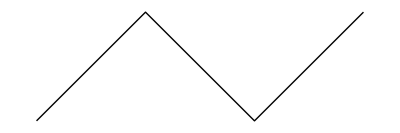

```mathematica
Graphics[Line[{{1,0},{2,1},{3,0},{4,1}}]]
```

Es posible combinar varias primitivas:

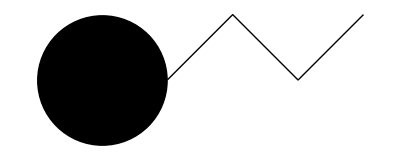

```mathematica
Graphics[{Disk[],Line[{{1,0},{2,1},{3,0},{4,1}}]}]
```

Y establecer directivas para cada una de las primitivas:

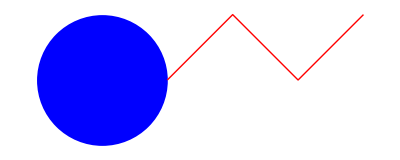

```mathematica
Graphics[{Blue,Disk[],Red,Thick,Line[{{1,0},{2,1},{3,0},{4,1}}]}]
```

Gráficas de funciones

Para efectos práctivos uno no suele utilizar las primitivas básicas ya que existen funciones que crean elementos gráficos de forma adecuada para graficar funciones. La gráfica más simple se puede crear con una función Plot, que grafica funciones definidas en los números reales.

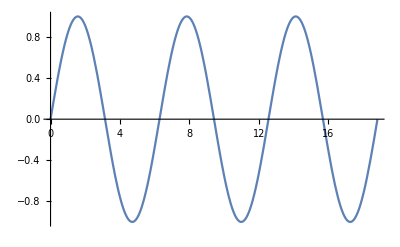

```mathematica
Plot[Sin[x],{x,0,6π}]
```

Para aumentar la cantidad de detalles que se muestra en la gráfica se pueden utilizar argumentos opcionales

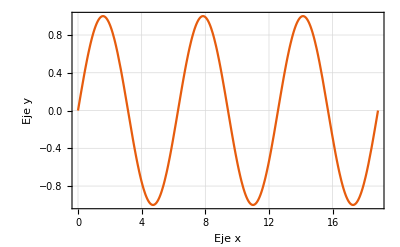

```mathematica
Plot[Sin[x],{x,0,6π},PlotTheme->"Scientific",FrameLabel->{"Eje x","Eje y"},GridLines->Automatic]
```

Algunas funciones discontinuas no se pueden graficar adecuadamente con Plot, para esto está DiscretePlot

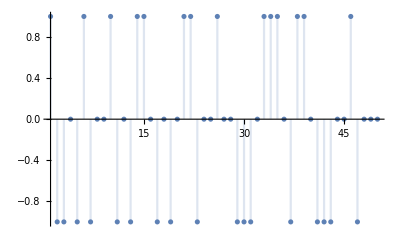
-Graphics--Graphics-

```mathematica
Row[{Plot[MoebiusMu[k],{k,1,50},ImageSize->400],DiscretePlot[MoebiusMu[k],{k,1,50},ImageSize->400]}]
```

Se pueden agrupar varias gráficas

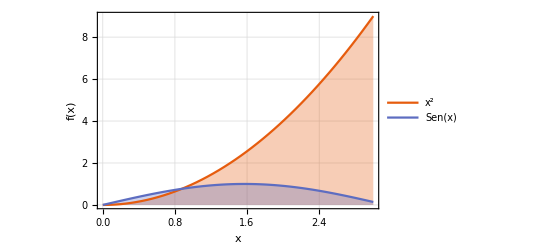

```mathematica
Plot[{x^2,Sin[x]},{x,0,3},PlotTheme->"Scientific", FrameLabel->{"x","f(x)"},ImageSize->400,BaseStyle->FontSize->16,GridLines->Automatic,Filling->Bottom,PlotLegends->{"x^2","Sen(x)"}]
```

Combinar gráficas a veces es útil para crear efectos

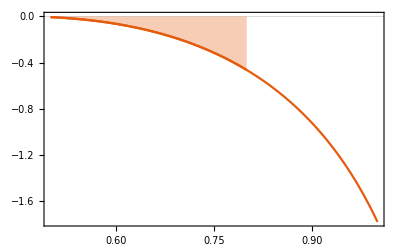

```mathematica
Show[
Plot[Log[Sin[Exp[x]]^2],{x,0.5,1},PlotTheme->"Scientific"],
Plot[Log[Sin[Exp[x]]^2],{x,0.5,0.8},Filling->Top,PlotTheme->"Scientific"]
]
```

Existen más tipos de gráficas que se pueden realizar, como gráficas en 3d

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},PlotTheme->"Scientific", AxesLabel->{"x","y","z"},BaseStyle->FontSize->16]
```

-Graphics3D-

Se pueden realizar gráficas implícitas. Nótese que la intersección coincide con la solución.

{{x→4.11111,y→2.88889}}

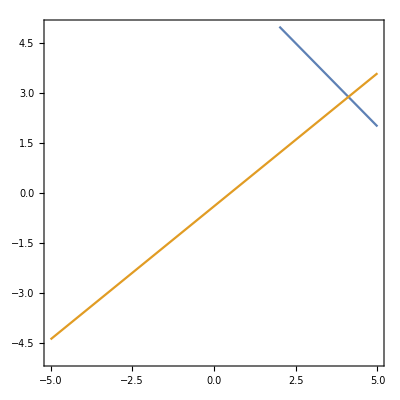

```mathematica
N[Solve[{x+y==7,4x-5y == 2},{x,y}]]
ContourPlot[{x+y==7,4x-5y == 2},{x,-5,5},{y,-5,5}]
```

#### Ejercicio 1:

Graficar

cos(x+y) = x,
y = x+2

y comprobar que la intersección coincide con la solución del sistema de ecuaciones.

Elementos interactivos

```mathematica
Manipulate[i^2,{i,0,10}]
```

```mathematica
Manipulate[
Plot[{x^2,Sin[a x]},
{x,0,3},
PlotTheme->"Scientific",
 FrameLabel->{"x","f(x)"},
ImageSize->400,
BaseStyle->FontSize->16,
GridLines->Automatic,
Filling->Bottom,
PlotLegends->{"x^2","Sen(ax)"}
],
{a,1,5}
]
```

#### Ejercicio

Crear un elemento interactivo que encuentre la solución de
Cos(x+y) = ax,
y = x+2,
donde a es un elemento variable de 1 a 2.